```mathematica
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=1
W[n_, z_ ] := Sum[ z^k/k! D2[n,k],{k,0,Log[2,n]}]
W1c[n_,z_] := Expand[FullSimplify[(W[n,z+1]-1)/(z+1)]]
```

```mathematica
N[W[100,1]]
```

303.601

```mathematica
D[W[100,z],z]
```

99+283 z+162 z^2+(92 z^3)/3+(17 z^4)/8+(7 z^5)/120

```mathematica
(-1/List@@NRoots[ W[100,x]==0,x][[All,2]])
```

{0.0419569-0.0288556 ⅈ,0.0419569+0.0288556 ⅈ,0.153113,0.266745,0.941024,97.5552}

```mathematica
(List@@NRoots[ W1c[100,x]==0,x][[All,2]])
```

{-17.1806-11.1282 ⅈ,-17.1806+11.1282 ⅈ,-7.53589,-4.73565,-2.08145}

```mathematica
vv:={-16.180664022748342-11.128144038617982 ⅈ,-16.180664022748342+11.128144038617982 ⅈ,-6.5311297858146515,-3.7489048140480477,-1.0626724626158177,-0.010250606310515099}
```

```mathematica
Sum[ -1/j,{j,vv}]
```

99.+0. ⅈ

```mathematica
vv2:={-17.18064807919592-11.128192517858471 ⅈ,-17.18064807919592+11.128192517858471 ⅈ,-7.535894740890104,-4.735647625732084,-2.081447189271695}
```

```mathematica
Product[1-1/j,{j,vv2}]
```

2.20238+0. ⅈ

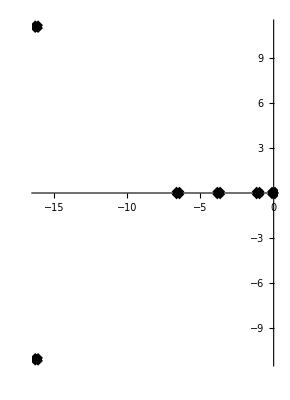

```mathematica
RootLocusPlot[1/Expand[W[100,x]],{k,0,1},FeedbackType->None]
```